CHAPTER ChapterLabel

Two-Dimensional Graphics and Plots

I’ve been looking so long at these pictures of you
that I almost believe that they’re real
I’ve been living so long with my pictures of you
that I almost believe that the pictures are all I can feel

The Cure, “Pictures of You”

ChapterLabel.Heading1  Introduction

One of the features that places Mathematica in a class by itself among similar computer-aided mathematics tools is its advanced graphics capabilities. This chapter focuses on two-dimensional graphics. Mathematica provides a variety of plotting functions with a versatile set of options for customizing their display. The most common types of 2D graphic are the plot of a function and list plots of values. Recipe 6.1 covers Plot and Recipe 6.4 covers ListPlot. Frequently you will want to use other coordinate systems or scales. In two dimensions, PolarPlot and ParametricPlot are often used as demonstrated in Recipes 6.1 and 6.2.

True to its symbolic nature, Mathematica represents all graphics as collections of graphics primitives and directives. Primitives include objects such as Point and Line; directives provide styling information such as Thickness and Hue. Mathematica allows you to work with the low-level primitives (see Recipe 6.8), but most readers will be interested in the higher-level functions like Plot and ListPlot, which generate graphics from functions and data and display them. However, it is easy to demonstrate that these functions generate primitives by specifying InputForm.

```mathematica
ListPlot[{0,1,2,3}]//InputForm
```

Graphics[{Hue[0.67, 0.6, 0.6], Point[{{1., 0.}, {2., 1.}, {3., 2.}, {4., 3.}}]}, {AspectRatio -> GoldenRatio^(-1), Axes -> True, AxesOrigin -> {0, Automatic}, PlotRange -> Automatic, PlotRangeClipping -> True}]

This uniform representation allows graphics to be manipulated programmatically, just like any Mathematica object, and sometimes can be useful for generating custom effects. However, this representation is not entirely at the lowest level, because graphics constructs like axes are implicitly specified via options. To get to the lowest level you can use the function FullGraphics. Here I use Short to suppress some of the details.

```mathematica
Short[InputForm[FullGraphics[ListPlot[{0,1,2,3}]]],10]
```

Graphics[{{Hue[0.67, 0.6, 0.6], Point[{{1., 0.}, {2., 1.}, {3., 2.}, {4., 3.}}]}, {{GrayLevel[0.], AbsoluteThickness[0.25], Line[{{0.2, 0.}, {0.2, 0.010112712429686845}}]}, Text[0.2, {0.2, -0.02022542485937369}, {0., 1.}], {GrayLevel[0.], AbsoluteThickness[0.25], Line[{{0.4, 0.}, {0.4, 0.010112712429686845}}]}, Text[0.4, {0.4, -0.02022542485937369}, {0., 1.}], {GrayLevel[0.], AbsoluteThickness[0.25], Line[{{0.6000000000000001, 0.}, {0.6000000000000001, 0.010112712429686845}}]}, Text[0.6000000000000001, {0.6000000000000001, -0.02022542485937369}, {0., 1.}], {GrayLevel[0.], AbsoluteThickness[0.25], Line[{{0.8, 0.}, {0.8, 0.010112712429686845}}]}, <<41>>, {GrayLevel[0.], <<2>>}, {GrayLevel[0.], AbsoluteThickness[0.125], Line[{{0., 0.9}, {0.00375, 0.9}}]}, {GrayLevel[0.], AbsoluteThickness[0.125], Line[{{0., 0.9500000000000001}, {0.00375, 0.9500000000000001}}]}, {GrayLevel[0.], AbsoluteThickness[0.25], Line[{{0., 0.}, {0., 1.}}]}}}]

In the recipes that follow, I make frequent use of GraphicsRow, GraphicsColumn, and GraphicsGrid. These are handy for formatting multiple graphics outputs across the page to make maximum use of both horizontal and vertical space. Both GraphicsRow and GraphicsColumn take a list of graphics to format, whereas GraphicsGrid takes a matrix. To help generate these lists and matrices, I sometimes use Table and Partition. These functions are simple enough that I hope they do not detract from the intended lesson of the recipe. Recipe 6.6 explains the use of these gridlike formatting functions in detail.

ChapterLabel.Heading1  Plotting Functions in Cartesian Coordinates

Problem

You want to graph one or more built-in or user-defined functions.

Solution

The simplest solution is to use the Plot command with the range of values to plot. Plot takes one or more functions of a single variable and an iterator of the form {var, min, max}.

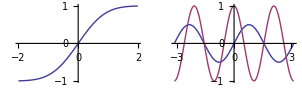

```mathematica
GraphicsRow[{
Plot[Erf[x],{x,-2,2}],
 Plot[{0.5 Sin[2 x],Cos[3 x]},{x, -Pi, Pi}]
}]
```

Discussion

Plot has a wide variety of options for controlling the appearance of the plot. Here are the defaults.

```mathematica
Partition[ Options[Plot] ,4]//TableForm
```

AlignmentPoint→Center | AspectRatio→1/GoldenRatio | Axes→True | AxesLabel→None
AxesOrigin→Automatic | AxesStyle→{} | Background→None | BaselinePosition→Automatic
BaseStyle→{} | ClippingStyle→None | ColorFunction→Automatic | ColorFunctionScaling→True
ColorOutput→Automatic | ContentSelectable→Automatic | CoordinatesToolOptions→Automatic | DisplayFunction:>$DisplayFunction
Epilog→{} | Evaluated→Automatic | EvaluationMonitor→None | Exclusions→Automatic
ExclusionsStyle→None | Filling→None | FillingStyle→Automatic | FormatType:>TraditionalForm
Frame→False | FrameLabel→None | FrameStyle→{} | FrameTicks→Automatic
FrameTicksStyle→{} | GridLines→None | GridLinesStyle→{} | ImageMargins→0.
ImagePadding→All | ImageSize→Automatic | ImageSizeRaw→Automatic | LabelStyle→{}
MaxRecursion→Automatic | Mesh→None | MeshFunctions→{#1&} | MeshShading→None
MeshStyle→Automatic | Method→Automatic | PerformanceGoal:>$PerformanceGoal | PlotLabel→None
PlotPoints→Automatic | PlotRange→{Full,Automatic} | PlotRangeClipping→True | PlotRangePadding→Automatic
PlotRegion→Automatic | PlotStyle→Automatic | PreserveImageOptions→Automatic | Prolog→{}
RegionFunction→(True&) | RotateLabel→True | Ticks→Automatic | TicksStyle→{}

When plotting two or more functions, you may want to explicitly set the style of each plot’s lines. You can also suppress one or both of the axes using Axes, as I do in the second and fourth plots. You can label one or both of the axes using AxesLabel and control the format using LabelStyle.

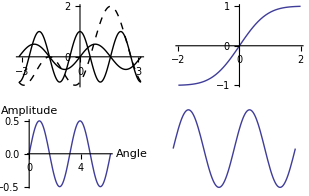

```mathematica
GraphicsGrid[{
{Plot[{0.5 Sin[2 x],Cos[3 x],Sin[x]-Cos[2x]},{x, -Pi, Pi},PlotStyle->{Directive[Black,Thin],Directive[Black,Thick],Directive[Black,Dashed]},ImageSize->Small],
Plot[Erf[x],{x,-2,2},Axes->{False,True}]},
{Plot[0.5 Sin[2 θ],{θ,0,2 π},AxesLabel-> {"Angle","Amplitude"},LabelStyle-> Directive[Bold],ImageSize->Small],
Plot[0.5 Sin[2 θ],{θ,0,2 π},Axes->False,ImageSize->Small]
}}]
```

PlotLabel is a handy option for naming plots, especially when you display several plots at a time.

```mathematica
GraphicsRow[{
Plot[Sin[x],{x,-2Pi,2Pi},PlotLabel->"Sin"],
Plot[Cos[x],{x,-2Pi,2Pi},PlotLabel->"Cos"]
}]
```

-Graphics-

You can add grid lines with an explicitly determined frequency or a frequency determined automatically by Mathematica.

```mathematica
GraphicsRow[{
Plot[Tan[x],{x,-Pi/2,Pi/2},GridLines->Automatic,ImageSize->Small,PlotLabel->"Automatic Grid"],Plot[Tan[x],{x,-Pi/2,Pi/2},GridLines->{{-Pi/2,-Pi/4,0,Pi/4,Pi/2},{-6,-4,-2,0,2,4,6}},ImageSize->Small,PlotLabel->"Custom Grid"]
}]
```

-Graphics-

Frame, FrameStyle, and FrameLabel let you annotate the graph with a border and label. Note that FrameStyle and FrameLabel only have effect if Frame→True is also specified.

```mathematica
GraphicsRow[{
Plot[Exp[Sin[x]],{x,0,2Pi},Frame->True,FrameLabel->"e^(sin x)",
ImageSize->Small],
Plot[Exp[Cos[x]],{x,0,2Pi},Frame->True,FrameLabel->"e^(cos x)",
FrameStyle->Directive[Gray,Thick],
ImageSize->Small]
}]
```

-Graphics-

Mesh is an option that allows you to highlight specific points in the plot. Mesh → All will highlight all points sampled while plotting the graph, Mesh → Full will use regularly spaced points. Mesh → n will use n equally spaced points. The behavior of Mesh → Automatic will vary based on the plotting primitive.

```mathematica
GraphicsGrid[Partition[Table[
Plot[0.5 Sin[2 θ],{θ,0,2 π},Mesh->m,
ImageSize->Small,Frame->True,
PlotLabel->"Mesh → " <> ToString[m]],
{m, {None,Automatic,All,Full,16,50}}],2],Spacings->0]
```

-Graphics-

PlotRange is an important option that controls what coordinates to include in the plot. Automatic lets Mathematica decide on the best choice, All specifies all points actually plotted, and Full specifies the entire range. In addition, you can supply explicit coordinates in the form {{xmin,xmax},{ymin,ymax}}.

```mathematica
GraphicsGrid[Partition[
Table[
Plot[Sqrt[100.0 -x^2],{x,0,100},PlotRange->r,ImageSize->{225,Automatic},Frame->True,FrameLabel->"PlotRange → " <> ToString[r]],
{r, {Automatic,All,Full,{{0,20},{0,20}}}}],2],Spacings->0]
```

-Graphics-

AspectRatio controls the ratio of height to width of the plot. The default value is 1/GoldenRatio (also known as ϕ). A value of Automatic uses the coordinate values to determine the aspect ratio.

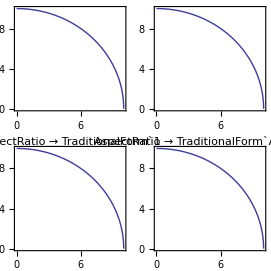

```mathematica
GraphicsGrid@Partition[
Table[
Plot[Sqrt[100.0 -x^2],{x,0,10},AspectRatio->a,Frame->True,FrameLabel->"AspectRatio → " <> ToString[TraditionalForm[a]]],
{a, {GoldenRatio^-1,Automatic,1.25,0.75}}],2]
```

Sometimes you want to emphasize an area on one side of the curve or between two different curves. Filling can be set to Top to fill from the curve upward, Bottom to fill from the curve downward, Axis to fill from the axis to the curve, or to a numeric value to fill from the curve to that value in either y direction.

```mathematica
GraphicsGrid@Partition[Table[
Plot[Sin[x],{x,0,2Pi},Filling->f,Frame->True,
FrameLabel->"Filling → " <> ToString[f],ImageSize->{200,Automatic}],
{f,{Top,Bottom,Axis,0.5}}],2]
```

-Graphics-

FillingStyle allows you to control the color and opacity of the filling. Specifying an opacity is useful where regions of multiple functions overlap.

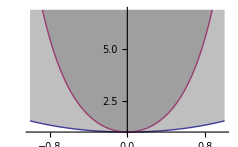

```mathematica
Plot[{Cosh[x],Cosh[3x]},{x,-1,1},Filling->Top,
FillingStyle->Directive[Gray,Opacity[0.5]],ImageSize->300]
```

You can also use a special notation to fill the area between two curves. In this notation, you refer to a curve by {i} where i is an integer referring to the ith plot. You can then say something like Filling → {i → {j}} to specify that filling should be between plot i and plot j. You can also override the FillingStyle by including a graphics directive, as in the example here.

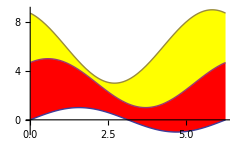

```mathematica
Plot[{Sin[x],2Sin[x+1]+3,3Sin[x+2]+6},{x,0,2Pi},
Filling->{1->{{2},Red},2->{{3},Yellow}},
ImageSize->300]
```

See Also

Recipes 6.2 and 6.3 demonstrate PolarPlot and ListPlot, which share most of the options of Plot.

ChapterLabel.Heading1  Plotting in Polar Coordinates

Problem

You want to create a plot in polar coordinates of radius as a function of angle.

Solution

Use PolarPlot, which plots the radius as the angle in polar coordinates varies counterclockwise with 0 at the x-axis, π/2 at the y-axis, and so on.

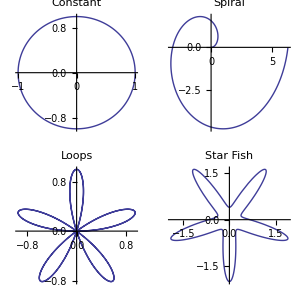

```mathematica
GraphicsGrid[{
{PolarPlot[1,{θ,0,2π},PlotLabel->"Constant"],
PolarPlot[θ,{θ,0,2π},PlotLabel->"Spiral"]},
{PolarPlot[Sin[5θ],{θ,0,2π},PlotLabel->"Loops"],
PolarPlot[1/(1.5+Sin[5θ]),{θ,0,2π},PlotLabel->"Star Fish"]}
}]
```

Discussion

As with Plot, you can plot several functions simultaneously.

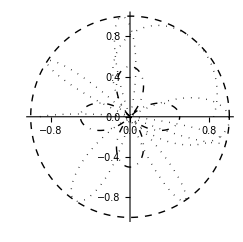

```mathematica
PolarPlot[{1,0.5Cos[2θ],Sin[Exp[θ/2]]},{θ,0,2π},
ImageSize->300,
PlotStyle->{Directive[Black,Dashed],
Directive[Black,DotDashed],
Directive[Black,Dotted]}]
```

The options for PolarPlot are essentially the same as Plot. One notable exception is the absence of options related to Filling. Also note that AspectRatio is automatic by default, which makes sense because symmetry is an essential aesthetic of polar plots.

```mathematica
Complement[Options[PolarPlot],Options[Plot]]
```

{AspectRatio→Automatic,Axes→Automatic,AxesOrigin→{0,0},MeshFunctions→{#3&},PlotRange→Automatic,PolarAxes→False,PolarAxesOrigin→Automatic,PolarGridLines→None,PolarTicks→Automatic}

ChapterLabel.Heading1  Creating Plots Parametrically

Problem

You want to create Lissajous curves and other parametric plots where points {fx[u], fy[u]} are plotted against a parameter u.

Solution

Here are some common Lissajous curves. Note how ParametricPlot takes a pair of functions in the form of a list.

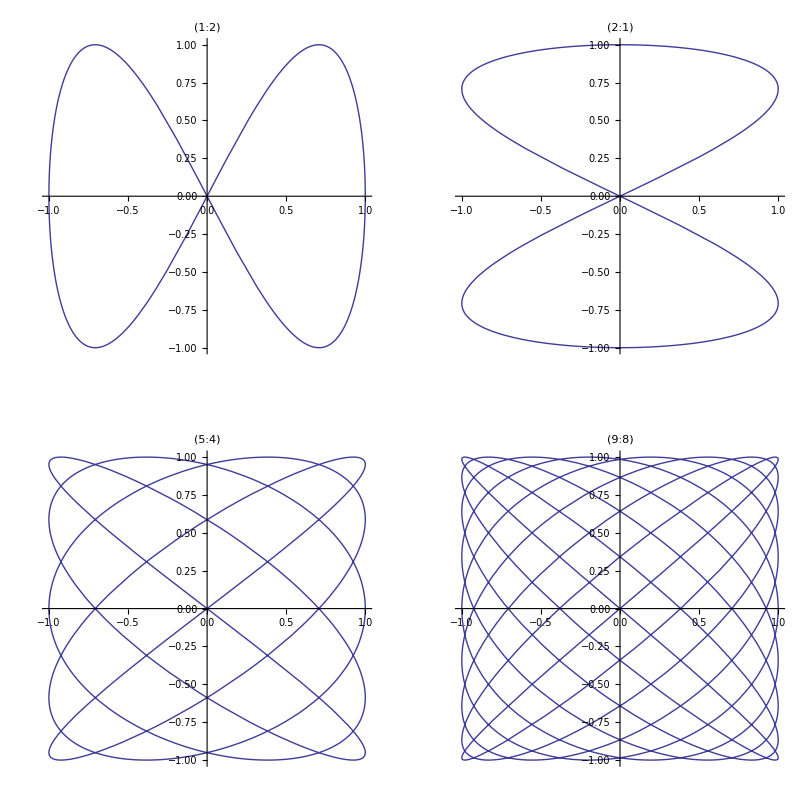

```mathematica
GraphicsGrid[{{ParametricPlot[{Sin[Pi u],Sin[2 Pi u]},{u,0,2},PlotLabel->"(1:2)"],
ParametricPlot[{Sin[2Pi u],Sin[ Pi u]},{u,0,2},PlotLabel->"(2:1)"]},
{ParametricPlot[{Sin[5Pi u],Sin[4 Pi u]},{u,0,2},
PlotLabel->"(5:4)"],
ParametricPlot[{Sin[9Pi u],Sin[8 Pi u]},{u,0,2},PlotLabel->"(9:8)"]}}]
```

Discussion

Here is an animation showing the effect of phase shifting on signals of frequency  ratio 1:1 and 2:1.

```mathematica
Animate[GraphicsRow[{ParametricPlot[{Sin[Pi u + d],Sin[ Pi u]},{u,0,2}],
ParametricPlot[{Sin[2 Pi u + d],Sin[ Pi u]},{u,0,2}]
}],{d,0,2Pi}]
```

You also use ParametricPlot to create parametric surfaces. This introduces a second parameter.

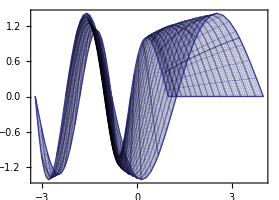

```mathematica
ParametricPlot[{ r^2 Cos[Sqrt[ t]],Sqrt[ r] Sin[r t]},{t,0,2Pi},{r,1,2}]
```

See Also

The 3D counterpart to ParametricPlot, ParametricPlot3D, is covered in Recipe 7.5.

ChapterLabel.Heading1  Plotting Data

Problem

You want to graph data values that were captured outside Mathematica or previously computed within Mathematica.

Solution

Use ListPlot with either lists of x values or lists of (x,y) pairs. In this first plot, I generate the y values but let the x values derive from the iteration range. You can also explicitly provide the x and y values as a pair for each point plotted, as shown in the second ListPlot, which compares PrimePi to Prime.

```mathematica
GraphicsRow[{
ListPlot[Table[Prime[i]/(1+Log[Fibonacci[i]]),{i,1,100}],ImageSize->250],
ListPlot[Table[{PrimePi[i],Prime[i]},{i,1,200}],ImageSize->250]
}]
```

-Graphics-

Discussion

ListPlot shares most options with Plot; instead of repeating them here, I show only the differences.

```mathematica
Complement[Options[ListPlot],Options[Plot]]
```

{DataRange→Automatic,InterpolationOrder→None,Joined→False,MaxPlotPoints→∞,PlotMarkers→None,PlotRange→Automatic}

DataRange allows you to specify minimum and maximum values for the x-axis. In the first plot, the x-axis is assumed to be integer values.

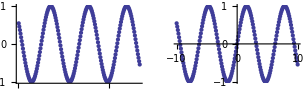

```mathematica
data = Table[Sin[x], {x, -10, 10, 0.1}];GraphicsRow[{ListPlot[data],ListPlot[data,DataRange->{-10,10}]},ImageSize->500]
```

InterpolationOrder is used with Joined to control the way lines drawn between points are interpolated. A value of 1 results in straight lines; higher values result in smoothing, although for most practical purposes, a value of 2 is sufficient.

```mathematica
data=RandomReal[{0,2},8];
GraphicsColumn[Table[ListPlot[data, Joined -> True, InterpolationOrder -> i,PlotLabel->("InterpolationOrder" <> ToString[i]),ImageSize->Small],{i,{1,2,3}}]]
```

-Graphics-

See Also

Mathematica has related list plotting functions ListLinePlot, ListLogLogPlot, and ListLogLinearPlot that have similar usage to ListPlot but are specialized for certain types of data. Refer to the Mathematica documentation to learn more.

ChapterLabel.Heading1  Mixing Two or More Graphs  into a Single Graph

Problem

You want to mix several kinds of plots into a single graph.

Solution

Use Show to combine graphs produced by different functions.

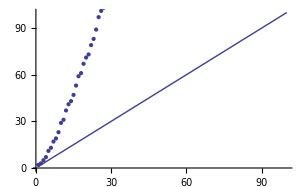

```mathematica
Show[Plot[x,{x,1,100}],ListPlot[Table[Prime[x],{x,1,100}]]]
```

Discussion

When using Show to combine plots, you can override options used in the individual graphs. For example, you can override the position of axes, aspect ratio, and plot range.

```mathematica
g1 = Plot[x^2 - x,{x,1,10},AspectRatio->0.6,AxesOrigin->Automatic];
g2 = Plot[x^2 + x,{x,1,10},AspectRatio->0.6,AxesOrigin->Automatic];
```

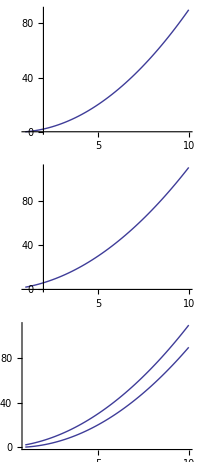

```mathematica
GraphicsColumn[{g1,g2,Show[g1,g2,AspectRatio->1,AxesOrigin->{0,0},PlotRange->All]},ImageSize->200]
```

Show can be used to combine arbitrary graphics. For example, you can give a graphic a background image.

```mathematica
g1 =Import[FileNameJoin[{NotebookDirectory[],"..","images","truck.jpg"}],"Graphics"];
g1 = Graphics[{Opacity[0.3],g1[[1]]}]; (*Insert opacity directive into graphics.*)
Show[Plot[x,{x,0,100},PlotStyle->Thick],g1,PlotRange->All,ImageSize->Small]
```

-Graphics-

One of my favorite mathematical illustrations is convergence through the iteration of a function (something I am sure many of you have done by repeatedly pressing Cos on a pocket calculator). Here, NestList performs 12 iterations. We duplicate every two and flatten and partition into pairs with overhand of 1 to yield the points for illustrating the convergence of the starting point 1 to the solution of x == Cos[x].

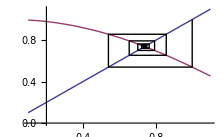

```mathematica
Show[Plot[{x, Cos[x]}, {x, 0.1, 1.1}], Graphics[Line[Partition[Flatten[{#, #} & /@ NestList[Cos, 1.0, 12]], 2, 1]]]]
```

Show uses the following rules to combine plots:

Use the union of plot intervals.

Use the value of Options from the first plot unless overridden by Show’s own options.

ChapterLabel.Heading1  Displaying Multiple Graphs in a Grid

Problem

You want to display several related graphs for easy comparison.

Solution

Use GraphicsGrid in Mathematica 6 or GraphicsArray in earlier versions. You can use tables to group several plots together, but this gives you very little control of the layout of the images. GraphicsGrid gives control of the dimensions of the grid, the frame, spacing, dividers, and other options. The dimensions of the grid are inferred from the dimensions of the list of graphics passed as the first argument. You will find Partition handy for converting a linear list into the desired two-dimensional form.

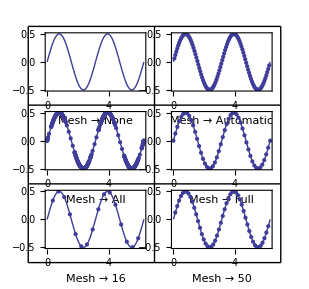

```mathematica
With[{cols =2},
GraphicsGrid[
Partition[Table[Plot[0.5 Sin[2 θ],{θ,0,2 π},
Mesh->m,ImageSize->Small,Frame->True,
FrameLabel->"Mesh → " <> ToString[m]],
{m, {None,Automatic,All,Full,16,50}}],
cols],Frame->All]
]
```

Discussion

In addition to GraphicsGrid, Mathematica provides GraphicsRow and GraphicsColumn, which are simpler to use for laying out graphics horizontally or vertically. These layout functions can be combined and nested to create more complex layouts. Here I demonstrate using GraphicsRow to show a GraphicsColumn next to another GraphicsRow. Frames can be drawn around the row or column (Frame→True) or additionally dividing all the elements (Frame→All).

```mathematica
With[{polygons =Table[
Graphics[{EdgeForm[Black],FaceForm[LightGray],
Polygon[Table[{Cos[2Pi k /p],Sin[2Pi k /p]},{k,p}]]},ImageSize->Tiny],
{p,4,8,2}]},
GraphicsRow[{
GraphicsColumn[polygons,Frame->True],
GraphicsRow[polygons,Frame->True]
},Frame->All,ImageSize->450]]
```

-Graphics-

ChapterLabel.Heading1  Creating Plots with Legends

Problem

You want to identify the information in a plot of multiple data sets using a legend.

Solution

Use the PlotLegends` package with the PlotLegend, LegendPosition, and LegendSize options.

```mathematica
Needs["PlotLegends`"];
Plot[{Sin[x],Sin[2x]},{x,0,2Pi},
PlotStyle->{Directive[Black,Dotted],Directive[Black,Dashed]},
PlotLegend->{"Sin x","Sin 2x"},
LegendPosition-> {1,0.1},LegendSize->0.75]
```

-Graphics-

Legends use their own coordinate system, for which the center of the graphic is at {0,0} and the inside is the scaled bounding region {{-1,-1},{1,1}}. LegendPosition refers to the lower left corner of the legend.

Discussion

There are a variety of options for further tweaking the legend’s appearance. You can turn off or control the offset of the drop shadow (LegendShadow); control spacing of various elements using LegendSpacing, LegendTextSpace, LegendLabelSpace, and LegendBorderSpace; control the labels with LegendTextDirection, LegendTextOffset, LegendSpacing, and LegendTextSpace; and give the legend a label with LegendLabel and LegendLabelSpace.

Notice the effect of LegendTextSpace, which is a bit counterintuitive because it expresses the ratio of the text space to the size of a key box so larger numbers actually shrink the legend. LegendSpacing controls the space around each key box on a scale where the box size is 1.

```mathematica
plotCommonOptions = Sequence[PlotStyle->{Directive[Black,Dotted],Directive[Black,Dashed]},
PlotLegend->{"Sin x","Sin 2x"},LegendPosition-> {1,0.1},LegendSize->0.75,ImageSize->250];

GraphicsGrid[{
{Plot[{Sin[x],Sin[2x]},{x,0,2Pi},
Evaluate[plotCommonOptions],
LegendShadow->None,
LegendSpacing->1/2,LegendTextSpace->10],
Plot[{Sin[x],Sin[2x]},{x,0,2Pi},
Evaluate[plotCommonOptions],
LegendShadow->None,LegendLabel->"Plots",
LegendSpacing->0.2,LegendTextSpace->5]
},
{Plot[{Sin[x],Sin[2x]},{x,0,2Pi},
Evaluate[plotCommonOptions],
LegendShadow->{-0.1,-0.1},LegendLabel->"Plots",
LegendSpacing->0.2,LegendTextSpace->5],
Plot[{Sin[x],Sin[2x]},{x,0,2Pi},
Evaluate[plotCommonOptions],
LegendShadow->{0.1,0.1},
LegendSpacing->1/2,LegendTextSpace->10]
}
}, 
Dividers->All]
```

See Also

Sometimes you want to create a more customized legend. In that case, consider  Legend and ShowLegend.

See the tutorial on the PlotLegends` package at http://bit.ly/TYvfV.

ChapterLabel.Heading1  Displaying 2D Geometric Shapes

Problem

You want to create graphics that contain lines, squares, circles, and other geometric objects.

Solution

Mathematica has a versatile collection of graphics primitives: Text, Polygon, Rectangle, Circle, Disk, Line, Point, Arrow, Raster, and Point can be combined to create a variety of 2D drawings. Here I demonstrate a somewhat frivolous yet instructive function that creates a snowman drawing using a broad sampling of the available primitives. Included is a useful function, ngon, for creating regular polygons.

```mathematica
ClearAll[generateSnow]
```

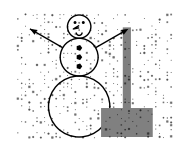

```mathematica
(*Create a regular polygon.*)
ngon[sides_Integer,center_List,size_?NumberQ,rotation_: 0 ]:=Polygon[Table[{size Cos[2Pi k/sides+rotation]+center[[1]],size Sin[2Pi k/sides+rotation]+center[[2]]},{k,sides}]]
(*Generate snow as randomly scattered pairs of semitransparent points of random size.*)
generateSnow[minPoint_List,maxPoint_List,density_?NumberQ] := Module[{size,z=100,j},{Opacity[0.3],Reap[Do[Which[RandomReal[]<0.3,
size=RandomReal[{0.001,0.008}];
j=RandomReal[{-1.0,1.0}];
Sow[{PointSize[size/1.3],If[RandomReal[]<0.5,{Point[{x,y+z size +j }],Point[{x,y-z size +j}],Point[{x+z size,y +j }],Point[{x-z size,y+j}]},{Point[{x+z size,y+z size +j }],Point[{x-z size,y+z size +j}],Point[{x+z size,y-z size +j }],Point[{x-z size,y-z size+j}]}],PointSize[size],Point[{x,y+j}]}]],{x,minPoint[[1]],maxPoint[[1]],density},{y,minPoint[[2]],maxPoint[[2]],density}]][[2,1]]}]
(*Draw a snowman whose base is of the given radius.*)
snowman[bodyRadius_] := Module[{bodyCenter = {0,0},
(*Proportioning the torso and head based on golden ratio gives a pleasing effect.*)
torsoRadius = bodyRadius /  GoldenRatio, 
headRadius= bodyRadius / (GoldenRatio^2),
torsoCenter,headCenter,leftShoulder,rightShoulder,
buttonSize = bodyRadius/10,buttonSep  = bodyRadius/3.3,
leftHand,rightHand,mouthCenter,leftEyeCenter,rightEyeCenter},
torsoCenter = {bodyCenter[[1]],torsoRadius+bodyRadius};
headCenter = {bodyCenter[[1]],bodyRadius+ 2 torsoRadius +headRadius};
(*Position the arms at -60 and 60 degrees.*)
leftShoulder = torsoCenter + {torsoRadius *Sin[-Pi/3],torsoRadius * Cos[-Pi/3]};
leftHand =  torsoCenter + {3torsoRadius *Sin[-Pi/3],3torsoRadius * Cos[-Pi/3]};
rightShoulder = torsoCenter + {torsoRadius *Sin[Pi/3],torsoRadius * Cos[Pi/3]};
rightHand = torsoCenter + {3torsoRadius *Sin[Pi/3],3torsoRadius * Cos[Pi/3]};
(*Position eyes at -45 and 45 degrees and half the radius of the head.*)
leftEyeCenter = headCenter + {0.5 headRadius * Sin[-Pi/4],0.5 headRadius * Cos[-Pi/4]};
rightEyeCenter = headCenter + {0.5 headRadius * Sin[Pi/4],0.5 headRadius * Cos[Pi/4]};
(*Position mouth at 180 degrees - bottom of circle. Also half radius of head.*)
mouthCenter = headCenter + {0.5 headRadius * Sin[Pi],0.5 headRadius * Cos[Pi]};
Graphics[{
Circle[bodyCenter,bodyRadius], (*base ciricle*)
Circle[torsoCenter,torsoRadius], (*middle circle*)
Circle[headCenter,headRadius], (*head*)
Circle[mouthCenter,headRadius/4,{-Pi,0}], (*half circle for mouth*)
(*Use disks for eyes.*)
Disk[leftEyeCenter,headRadius/8],
Disk[rightEyeCenter,headRadius/8],
(*Make a carrot-shaped nose out of lines. The proportions here were worked out by trial and error.*)
Line[{headCenter - {0,headRadius/10},headCenter-{headRadius/2,headRadius/5},headCenter + {0,headRadius/10}}],
(*I use arrows for arms to illustrate how they work. See discussion for more detail.*)
{Arrowheads[{-0.1,0}],Arrow[{leftHand,leftShoulder}]},
{Arrowheads[{0,0.1}],Arrow[{rightShoulder,rightHand}]},
{Gray,Thickness[torsoRadius/800],Line[{rightHand+{-2,2},{rightHand[[1]]-2,-bodyRadius/2}}],Rectangle[bodyCenter+{bodyRadius/1.4,-2},bodyCenter+{2.4bodyRadius,-bodyRadius}]},
generateSnow[{-2bodyRadius,-bodyRadius},{3 bodyRadius,3.1 bodyRadius},5],
(*Use pentagons to simulate coal buttons.*)
ngon[5,{0,torsoRadius+bodyRadius-buttonSep},buttonSize],ngon[5,{0,torsoRadius+bodyRadius},buttonSize],ngon[5,{0,torsoRadius+bodyRadius+buttonSep},buttonSize]},ImageSize->bodyRadius*10]]
snowman[40]
```

Discussion

One of the keys to getting the most out of the graphics primitives is to learn how to combine them with graphics directives. Some directives are very specific, whereas others are quite general. For example, Arrowheads applies only to Arrow, whereas Red and Opacity apply to all primitives. A directive will apply to all objects that follow it, subject to scoping created by nesting objects within a list. For example, in the following graphic, Red applies to Disk and Rectangle but not Line because the line is given a specific color and thickness within its own scope.

```mathematica
Graphics[{Red,Disk[{-2,-2},0.5],Rectangle[],{Thickness[0.02],Black,Line[{{-1.65,-1.65},{0,0}}]}},ImageSize->Small]
```

-Graphics-

Color directives can use named colors: Red, Green, Blue, Black, White, Gray, Cyan, Magenta, Yellow, Brown, Orange, Pink, Purple, LightRed, LightGreen, LightBlue, LightGray, LightCyan, LightMagenta, LightYellow, LightBrown, LightOrange, LightPink, and LightPurple. You can also synthesize colors using RGBColor or Hue, CMYKColor, GrayLevel, and Blend. In Mathematica 6 or later versions, these directives can take opacity values in addition to values that define the color or gray settings. Blend is also new to Mathematica 6.

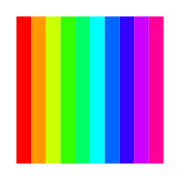

```mathematica
Graphics[Table[{Hue[x],Rectangle[{x,1},{x+0.1,2}]},{x,0,0.99,.1}],ImageSize->Small]
```

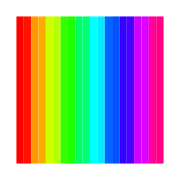

```mathematica
Graphics[Table[{Hue[x],Rectangle[{x,1},{x+0.05,2}],Blend[{Hue[x],Hue[x+0.05]},0.25],Rectangle[{x+.05,1},{x+0.1,2}]},{x,0,0.99,.1}],ImageSize->Small]
```

Of course, you’ll need to try the code on your own to view the colors.

Thickness[r] is specified relative to the total width of the graphic and, therefore, scales with size changes. AbsoluteThickness[d] is specified in units of printer points (1/72 inch) and does not scale. Thick and Thin are predefined versions (0.25 and 2, respectively) of AbsoluteThickness. Thickness directives apply to primitives that contain lines such as Line, Polygon, Arrow, and the like.

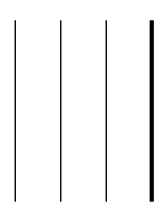

```mathematica
Graphics[{Line[{{0,-1},{0,1}}],{Thin,Line[{{0.5,-1},{0.5,1}}]},{Thick,Line[{{1,-1},{1,1}}]},{AbsoluteThickness[3],Line[{{1.5,-1},{1.5,1}}]}}]
```

See Also

Recipe 14.12 applies Mathematica’s graphics primitives to the serious task of visualizing Hull-White trees, which are used in modeling interest-rate-sensitive securities.

Recipe 13.11 shows an application in constructing finite element diagrams used in engineering.

ChapterLabel.Heading1  Annotating Graphics with Text

Problem

You want to add stylized text to graphics.

Solution

Use Text with Style to specify FontFamily, FontSubstitutions, FontSize, FontWeight, FontSlant, FontTracking, FontColor, and Background.

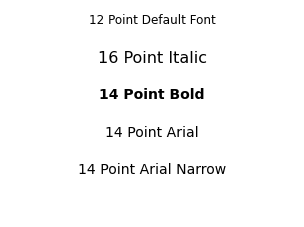

```mathematica
Graphics[{Text[Style["12 Point Default Font",FontSize->12],{0,0}],Text[Style["16 Point Italic",FontSize->16,FontSlant->Italic],{0,-.2}],
Text[Style["14 Point Bold",FontSize->14,FontWeight->Bold],{0,-.4}],
Text[Style["14 Point Arial",FontSize->14,FontFamily->"Arial"],{0,-.6}],
Text[Style["14 Point Arial Narrow",FontSize->14,FontFamily->"Arial",FontTracking->"Narrow"],{0,-.8}],
Text[Style["14 Point Bold White on Black",FontSize->14,FontWeight->Bold,FontColor->White,Background->Black],{0,-1}]},ImageSize->Small]
```

Discussion

In this chapter, I demonstrate various plotting functions that contain options for adding labels to the entire graph, frames, and axes. These options can also be stylized.

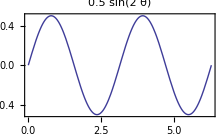

```mathematica
Plot[0.5 Sin[2 θ],{θ,0,2 π},PlotLabel-> Style[0.5 Sin[2 θ],FontSize->20,FontFamily->"Arial"],AxesLabel-> {"Radians","Amplitude"},LabelStyle-> Directive[Bold,FontFamily->"Arial",FontSize->12],Frame->True,FrameLabel->Style["Sine Wave",FontSlant->Italic],ImageSize->Medium]
```

The Style directive was added into Mathematica 6 and is quite versatile. Style can add style options to both Mathematica expressions and graphics.

ChapterLabel.Heading1  Creating Custom Arrows

Problem

You want to create arrows with custom arrowheads, tails, and connecting lines for use in annotating graphics.

Solution

Use Arrowheads with a custom graphic to create arbitrary arrowheads and tails.

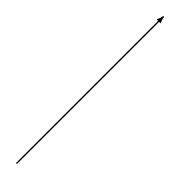

```mathematica
With[{h= Graphics[{Disk[{0,0},0.75]}],t =  Graphics[{Line[{{-0.5,0},{0.5,0}}],Line[{{0,-0.6},{0,0.6}}],Line[{{0.2,-0.6},{0.2,0.6}}]}]},
Graphics[{Arrowheads[{{0.05,1,h},{0.1,0,t}}],Arrow[{{0,0},{0.25,0.25}}]},ImageSize->Small]]
```

Discussion

Arrowheads is quite versatile. You can easily create double-ended arrows and arrows with multiple arrowheads along the span.

```mathematica
Graphics[{Arrowheads[{-0.1,0.1}],Arrow[{{0,0},{1,0}}],
Arrowheads[{0,0.1,.1,.1,.1}],Arrow[{{0,-0.5},{1,-0.5}}]},
ImageSize->Small]
```

You may consider using Arrowheads to label arrows, but Mathematica does not treat such “arrowheads” specially, so you may get undesirable effects.

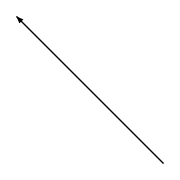

```mathematica
Graphics[{Arrowheads[{0,{Automatic,0.5,Graphics[{Text[Style["Label",FontSize->14,FontWeight->Bold]]}]},0.1}],Arrow[{{0,0},{-0.25,0.25}}]},ImageSize->Small]
```

A better option is to position the text by using Rotate with Text or Inset or by using GraphPlot or related functions (see Recipe 4.6). The advantage of Inset over manually positioned Text is that you get auto-centering if you don’t mind the label not being parallel to the arrow.

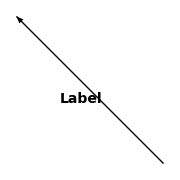

```mathematica
Graphics[{Arrowheads[{0.1}],Arrow[{{0,0},{-0.25,0.25}}],Rotate[Text[Style["Label",FontSize->14,FontWeight->Bold],{-0.14,0.11}],-Pi/4]},ImageSize->Small]
```

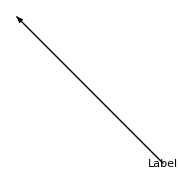

```mathematica
Graphics[{Arrowheads[{0.1}],Arrow[{{0,0},{-0.25,0.25}}],Inset[Text[Style["Label",FontSize->14,FontWeight->Bold]]]},ImageSize->Small]
```